## Kinetic

```mathematica
Subscript[v, T]=Sqrt[0.01];
Subscript[v, D]=0.3;
k=0.4;
c=1.0;
Subscript[ω, 0]=1.0;Z[ζ_] := ⅈ Sqrt[π] Exp[-ζ^2] (1+Erf[ⅈ ζ]);ζ[ω_]:=1/Sqrt[2 Subscript[v, T]^2] ω/(Subscript[ω, 0] k);
```

```mathematica
guess = 0.1  ⅈ;
root=FindRoot[0.5==Subscript[ω, 0]^2/(c^2 k^2)(ζ[ω] Z[ζ[ω]](1+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, T]^2/c^2 ζ[ω] *ζ[ω] ,{ω, guess}]
```

{ω→0.+0.103518 ⅈ}

## Fluid

```mathematica
Γ = 1/Sqrt[1-Subscript[v, D]^2/c^2];
Subscript[Ω, 1][ω_]:= 1/(Γ ω^2)
Subscript[Ω, 2][ω_]:= 1/(Γ^3 ω^2)
Subscript[Ω, 3][ω_]:= 0
Subscript[Ω, 4][ω_]:= Subscript[v, D]^2/(Γ ω^2)
```

```mathematica
FindRoot[0 == ω^2(1-Subscript[Ω, 2][ω])(1-Subscript[Ω, 1][ω])-k^2((1-Subscript[Ω, 1][ω])(1+Subscript[Ω, 4][ω])+(Subscript[Ω, 3][ω])^2), {ω, 0.1ⅈ}]
```

{ω→0.+0.111805 ⅈ}

## Plotting

```mathematica
ks =Table[i/10,{i,100}];
roots = Table[0,{i,100}];
k=ks[[1]];
guess = 0.05ⅈ;
root=FindRoot[0.5==Subscript[ω, 0]^2/(c^2 k^2)(ζ[ω] Z[ζ[ω]](1+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, T]^2/c^2 ζ[ω] *ζ[ω] ,{ω, guess}];
roots[[1]]=ω/.root[[1]];
For[i=2,i≤100,i++,k=ks[[i]];guess=roots[[i-1]];root=FindRoot[0.5==Subscript[ω, 0]^2/(c^2 k^2)(ζ[ω] Z[ζ[ω]](1+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, D]^2/Subscript[v, T]^2)+Subscript[v, T]^2/c^2 ζ[ω] *ζ[ω] ,{ω, guess}];roots[[i]]=ω/.root[[1]];]
```

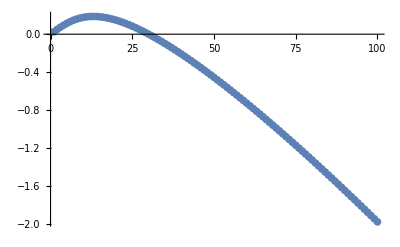

```mathematica
ListPlot[Im[roots]]
```